# T e a m A n h a r m o n i c a

# Sr.no. | Name | Roll no. 1 | Niraj Atale | 17162 2 | Piyush Paliwal© | 17180 3 | Ruchir Gupta | 17229 4 | Yash Mandlecha | 17327

# PHY 208 : Mini-Project Coupled Anharmonic Oscillators - Damped and Forced

## Introduction: Where do we find Anharmonic Oscillations in Nature? There are many systems throughout the physical world that can be modelled as anharmonic oscillators in addition to the nonlinear mass-spring system with 2 blocks studied here. First of all, it is essential to understand the difference between a Harmonic and an Anharmonic Oscillator. We understand it better by portraying an explanation for the simple pendulum. The block attached to a spring is a classic example of harmonic oscillation. Depending on the block's location 'x', it will experience a restoring force toward the middle (Directly proportional to x). The restoring force is proportional to x, so the system exhibits simple harmonic motion. A pendulum swings back and forth. Here we use an approximation for very small oscillations of the pendulum where sin(θ) ~θ. Whereas, A pendulum for oscillations of considerably large amplitude is a simple anharmonic oscillator. Depending on the mass's angular position θ, a restoring force pushes coordinate θ back towards the middle. This oscillator is anharmonic because the restoring force is not proportional to θ, but to sin(θ). Because the linear function y=θ approximates the nonlinear function y=sin(θ) when θ is small, the system can be modelled as a harmonic oscillator for small oscillations. Anharmonicity plays a significant role in the lattice and molecular vibrations, in quantum oscillations, and in acoustics. The atoms in a molecule or a solid vibrate about their equilibrium positions. When these vibrations have small amplitudes they can be described by harmonic oscillators. However, when the vibrational amplitudes are large, for example at high temperatures, anharmonicity becomes important. An example of the effects of anharmonicity is the thermal expansion of solids. The ubiquitous phenomenon of thermal expansion cannot be explained within the harmonic theory of the crystal lattice. The reason is that the pressure of a gas of harmonic phonon ( a quasi-particle associated with vibration of a crystal lattice) is temperature-independent since the phonon frequency does not depend on the amplitude of the oscillations. However, by introducing an anharmonic term, the phonon gas acquires a finite temperature-dependent pressure, which is ultimately responsible for the thermal expansion of the crystal. The Graphs below represent the above description for the Di-molecular Vibrations and Thermal Expansion.

## -Graphics- -Graphics- Figure 1 Figure 2 The first figure (Figure 1) here shows comparison of harmonic approximation to potential energy surface with the more realistic Morse curve description. The energy levels predicted by the solution of the Schrödinger Equation are also shown.The harmonic potential is an excellent approximation to the Morse curve when the anharmonicity is very small. This condition is shown in the second figure (Figure 2). As anharmonicity is decreased, the dissociation energy increases, resulting in more bound energy levels for the Morse oscillator.

## Anharmonicity not only makes the potential experienced by each oscillator more complicated, but also introduces coupling between the oscillators. It is possible to use first-principles methods such as density-functional theory to map the anharmonic potential experienced by the atoms in both molecules and solids. Accurate anharmonic vibrational energies can then be obtained by solving the anharmonic vibrational equations for the atoms within a mean-field theory. Non-equilibrium semiconductors that possess a large hot carrier population, which exhibit nonlinear behaviors of various types related to the effective mass of the carriers are also a consequence of the Anharmonic Oscillator. Ionospheric plasmas, which also exhibit nonlinear behavior based on the anharmonicity of the plasma. In fact, virtually all oscillators become anharmonic when their pump amplitude increases beyond some threshold, and as a result it is necessary to use nonlinear equations of motion to describe their behavior. https://www2.physics.ox.ac.uk/sites/default/files/CrystalStructure_Handout9_2.pdf https://pubs.acs.org/doi/pdf/10.1021/ed082p1263.2

# We will be studying a system of 2 blocks (A and B) of the same mass 'M', attached to each other with a massless spring of spring constant 'k'. A force F(t) is applied horizontally to the block B. Different physical configurations correspond to different functions acting as the external force F(t). We now study this problem under some unique conditions, including some interesting modifications of this problem in nature.

# -Graphics-

Defining the 4^thorder Runge-Kutta Module function as follows:

```mathematica
rk4[F_,X0_,tf_,nMax_]:=Module[{h,rate1,rate2,rate3,rate4,next,prev,datalist},
h=(tf-X0[[1]])/nMax//N;
For[datalist={X0},
Length[datalist]≤nMax,
AppendTo[datalist,next],
prev=Last[datalist];
rate1=Through[F@@prev];
rate2=Through[F@@(prev+(h/2)rate1)];
rate3=Through[F@@(prev+(h/2)rate2)];
rate4=Through[F@@(prev+h rate3)];
next=prev+(h/6)(rate1+2 rate2+2 rate3 +rate4);
];
Return[datalist];
]
```

We convert  the 2^nd order differential equation obtained into  a 1^st order differential  equation by considering the following differential equations. They are,  (θ^(..))_A= (ω̇)_A and  (θ^(..))_B= (ω̇)_(B.)

```mathematica
The actual differential equations obtained in terms of Subscript[θ^(..), A] and Subscript[θ^(..), B] are:
{{..}, {Subscript[θ, A]}}  =-Sin[Subscript[θ, A]]+KL/Mg(1 - 2/r)  [2Cos[Subscript[θ, A]]  - Sin(Subscript[θ, A]- Subscript[θ, B])]
```

Syntax::sntxi: Incomplete expression; more input is needed .

## Case 1: - Initially Stretched System with Absence Damping Force and Driving Force a) θ_(0a) = θ_(0b) b) θ_(0a) = -θ_(0b) c)θ_(0a) and θ_(0b)are not equal

#### a) θ_(0a) = θ_(0b)

```mathematica
F[t_]=0;    initial1a={0,Pi/3,Pi/3,0,0};     f=0.0;              (* Case 1 *)
```

```mathematica
α=0.5;
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data1a=rk4[{Id,taDot,tbDot,waDot,wbDot},initial1a,100,5000];
```

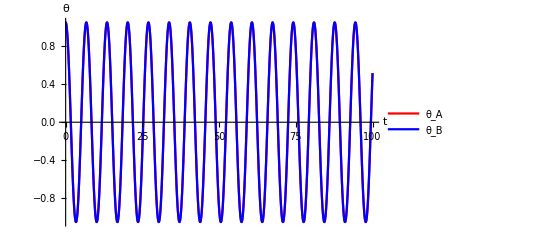

```mathematica
T1=ListPlot[data1a[[;;,{1,2}]],Joined->True,PlotRange->Full,PlotStyle->Red,PlotLegends->{Subscript[θ, A]}];
T2=ListPlot[data1a[[;;,{1,3}]],Joined->True,PlotRange->Full,PlotStyle->Blue,PlotLegends->{Subscript[θ, B]}];
Show[T1,T2,AxesLabel->{t,θ}]
```

#### b) θ_(0a) = -θ_(0b)

```mathematica
initial1b={0,Pi/6,-Pi/6,0,0};
```

```mathematica
data1b=rk4[{Id,taDot,tbDot,waDot,wbDot},initial1b,100,5000];
```

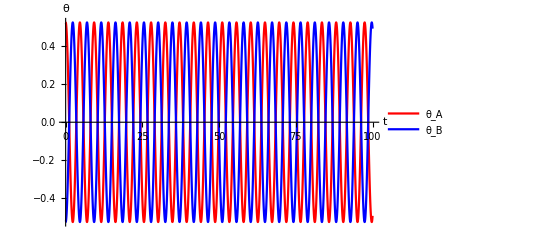

```mathematica
T1=ListPlot[data1b[[;;,{1,2}]],Joined->True,PlotRange->Full,PlotStyle->Red,PlotLegends->{Subscript[θ, A]}];
T2=ListPlot[data1b[[;;,{1,3}]],Joined->True,PlotRange->Full,PlotStyle->Blue,PlotLegends->{Subscript[θ, B]}];
Show[T1,T2,AxesLabel-> {t,θ}]
```

### c) θ_(0a) and θ_(0b) are not equal

```mathematica
initial1c={0,Pi/10,Pi/15,0,0};
```

```mathematica
data1c=rk4[{Id,taDot,tbDot,waDot,wbDot},initial1c,100,5000];
```

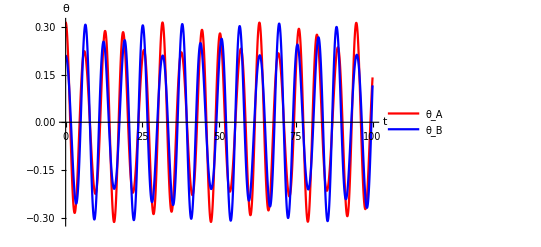

```mathematica
T1=ListPlot[data1c[[;;,{1,2}]],Joined->True,PlotRange->Full,PlotStyle->Red,PlotLegends->{Subscript[θ, A]}];
T2=ListPlot[data1c[[;;,{1,3}]],Joined->True,PlotRange->Full,PlotStyle->Blue,PlotLegends->{Subscript[θ, B]}];
Show[T1,T2,AxesLabel-> {t,θ}]
```

### Observation : 1) As spring is initially stretched so after releasing spring blocks starts oscillating. As there is no damping force and driving force present so it will oscillates with constant frequency. 2) The frequency with which system oscillates is called coupled oscillation frequency and as both blocks are out of phase a) First Plot Shows when pendulum are in phase when oscillating b) Second Plot shows When Pendulum are out of phase when oscillating c) Third plot shows when they are at random position

#### Physical System Related to this case : In order to study molecular vibrations, we can assume molecules to be coupled oscillators. Their Normal modes are of great importance in study of absorption and emission spectra. Above three are possible cases of molecular vibrations.

## Case 2: Presence of Damping force with initial stretched spring and No Driving Force Present ere three sub cases are possible: 1) Underdamped 2) Critically Damped 3) Overdamped

-Graphics-

Physical System: System submerged in a viscous medium. E.g. Acetone (Viscosity coefficient: 0.306 centipoise)

#### 1) Under Damped Oscillations (f < 2 ω_0)

```mathematica
F[t_] = 0;   initial={0,Pi/3,-Pi/3,0,0} ;   f=0.01;       (*  Underdamping case   *)(*  First Find out Natural Frequency of oscillations by putting f =0 to get an ide about damping frequency   *)
```

```mathematica
α=0.05;   
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data3a=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,100,5000];
```

```mathematica
FindFit[data3a[[;;,{1,2}]],{a Cos[b x]},{a,b},x]  (* To find the natural frequncy when f = 0  *)
```

{a→0.772024,b→0.986081}

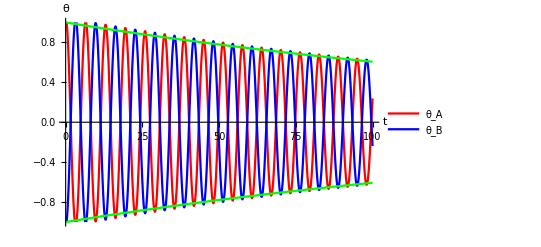

```mathematica
T1=ListPlot[data3a[[;;,{1,2}]],Joined->True,PlotRange->{-1,1},PlotStyle->Red,PlotLegends->{Subscript[θ, A]}];
T2=ListPlot[data3a[[;;,{1,3}]],Joined->True,PlotRange->{-1,1},PlotStyle->Blue,PlotLegends->{Subscript[θ, B]}];
Show[T1,T2,Plot[{Exp[-f x/2],-Exp[-f x/2]},{x,0,100},PlotStyle->Green],AxesLabel-> {t,θ}]
```

#### Critically Damped Oscillations (f = 2 ω_0)

```mathematica
F[t_] = 0;   initial={0,Pi/3,-Pi/3,0,0} ;   f=3.8418;       (*  First Find out Natural Frequency of oscillations by putting f =0 to get an ide about damping frequency   *)
```

```mathematica
α=0.005;   
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data3b=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,100,5000];
```

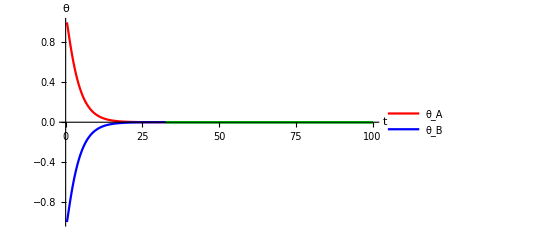

```mathematica
T1=ListPlot[data3b[[;;,{1,2}]],Joined->True,PlotRange->{-1,1},PlotStyle->Red,PlotLegends->{Subscript[θ, A]}];
T2=ListPlot[data3b[[;;,{1,3}]],Joined->True,PlotRange->{-1,1},PlotStyle->Blue,PlotLegends->{Subscript[θ, B]}];
Show[T1,T2,Plot[{Exp[-f x/2],-Exp[-f x/2]},{x,0,100},PlotStyle->Green],AxesLabel-> {t,θ}]
```

#### Over Damped Oscillations (f > 2 ω_0)

```mathematica
F[t_] = 0;   initial={0,Pi/3,-Pi/3,0,0} ;   f=4;       (*  First Find out Natural Frequency of oscillations by putting f =0 to get an ide about damping frequency   *)
```

```mathematica
α=1;   
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data3c=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,100,5000];
```

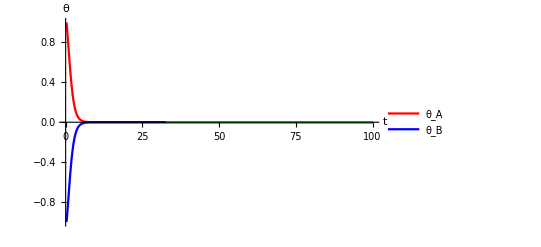

```mathematica
T1=ListPlot[data3c[[;;,{1,2}]],Joined->True,PlotRange->{-1,1},PlotStyle->Red,PlotLegends->{Subscript[θ, A]}];
T2=ListPlot[data3c[[;;,{1,3}]],Joined->True,PlotRange->{-1,1},PlotStyle->Blue,PlotLegends->{Subscript[θ, B]}];
Show[T1,T2,Plot[{Exp[-f x/2],-Exp[-f x/2]},{x,0,100},PlotStyle->Green],AxesLabel-> {t,θ}]
```

### Observation : 1) From our observation, Due to presence of air like resistance, Amplitude of system is decreasing and finally approaches to zero.

### Physical System: Driven RLC circuit is the best example related to these cases. Here Damping force is due to Resistor values. -Graphics-

## Case 3: - Sinusoidal Driving Force (with frequency ω) with rest conditions and No damping force Present a) ω < ω_0 b) ω ~ ω_0 (Resonance Condition) c) ω > ω_0 ( ω_0 is natural frequency of coupled oscillator)

### Here We have to attach One picture in which Plot of F(ω) Vs ω is shown and Formula and resonance condition is written

### a) ω < ω_0

```mathematica
ω = 0.4;               F[t_]=(1/2)Sin[ω t];                      initial3={0,0,0,0,0};                          f=0.0;
```

```mathematica
α=2;
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data3a=rk4[{Id,taDot,tbDot,waDot,wbDot},initial3,150,5000];
```

### Note: To get an Idea of approximate natural frequency of Coupled Oscillators, We can use Find fit to fit data into Sine Function according to our initial conditions and get the idea of range around which natural frequency lies.

```mathematica
FindFit[data3a[[;;,{1,2}]],{a Sin[b x]},{a,b},x]
```

{a→-0.109782,b→1.00713}

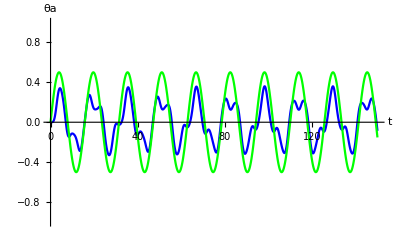

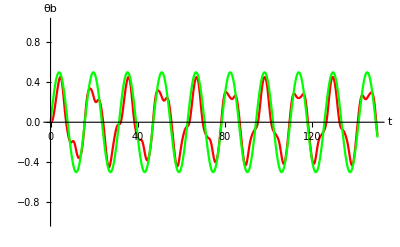

```mathematica
Shiv=Plot[F[t],{t,0,150},PlotRange->{-5,5},PlotStyle->Green];
Show[ListPlot[data3a[[;;,{1,2}]],Joined->True,PlotStyle->Blue,AxesLabel->{t,θa},LabelStyle->Directive[Blue,Bold],PlotRange->{-1,1}],Shiv]
Show[Theta2=ListPlot[data3a[[;;,{1,3}]],Joined->True,PlotStyle->Red,AxesLabel->{t,θb},LabelStyle->Directive[Blue,Bold],PlotRange->{-1,1}],Shiv]
Energy=Table[{data3a[[i, 1]],data3a[[i,4]]*data3a[[i,4]]},{i,1,Length[data3a]}];
ListPlot[{Energy[[;;,{1,2}]]},Joined->True];
```

### Observation: 1. We can observe random oscillation coupled pendulums with frequency about that of frequency of Driving Force. This system can't achieve steady state here due to absence of damping force. Which is true from plot obtained in this case.

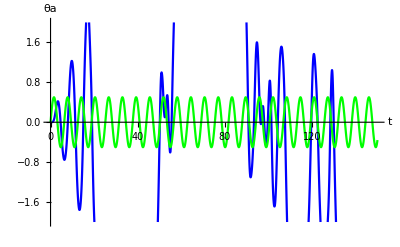

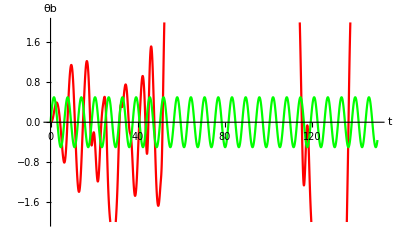

```mathematica
Shiv=Plot[F3b[t],{t,0,150},PlotRange->{-5,5},PlotStyle->Green];
Show[ListPlot[data3b[[;;,{1,2}]],Joined->True,PlotStyle->Blue,AxesLabel->{t,θa},LabelStyle->Directive[Blue,Bold],PlotRange->{-2,2}],Shiv]
Show[Theta2=ListPlot[data3b[[;;,{1,3}]],Joined->True,PlotStyle->Red,AxesLabel->{t,θb},LabelStyle->Directive[Blue,Bold],PlotRange->{-2,2}],Shiv]
Energy=Table[{data3b[[i, 1]],data3b[[i,4]]*data3b[[i,4]]},{i,1,Length[data3b]}];
ListPlot[{Energy[[;;,{1,2}]]},Joined->True];
```

### b) ω ~ ω_0 (Resonance Condition)

```mathematica
ω = 1;               F[t_]=(1/2)Sin[ω t];                      initial3={0,0,0,0,0};                          f=0.0;
```

```mathematica
α=2;
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data3a=rk4[{Id,taDot,tbDot,waDot,wbDot},initial3,150,5000];
```

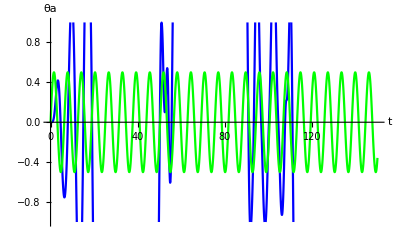

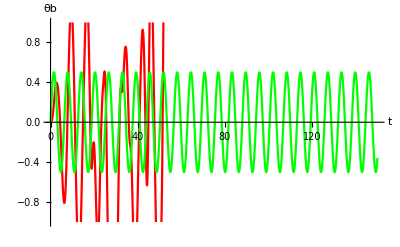

```mathematica
Shiv=Plot[F[t],{t,0,150},PlotRange->{-5,5},PlotStyle->Green];
Show[ListPlot[data3a[[;;,{1,2}]],Joined->True,PlotStyle->Blue,AxesLabel->{t,θa},LabelStyle->Directive[Blue,Bold],PlotRange->{-1,1}],Shiv]
Show[Theta2=ListPlot[data3a[[;;,{1,3}]],Joined->True,PlotStyle->Red,AxesLabel->{t,θb},LabelStyle->Directive[Blue,Bold],PlotRange->{-1,1}],Shiv]
Energy=Table[{data3a[[i, 1]],data3a[[i,4]]*data3a[[i,4]]},{i,1,Length[data3a]}];
ListPlot[{Energy[[;;,{1,2}]]},Joined->True];
```

### Observation: 2. At resonance There is sharp increase of amplitude of oscillator. This can easily be observe form plot shown here.

#### Importance Of resonance Condition: From the Plot we can observe that when frequency of driving force is equals to or close to natural frequency of the system, then Maximum energy is being transferred to the system as a result of which amplitude of system becomes large. E.g. Some example resonance is: 1. During parade as solider as advised to not to match frequency of steps otherwise the bridge may collapse due to energy transfer. -Graphics- 2. Opera singers can break a glass, just by adjusting their vocal frequency to the natural frequency of a glass. -Graphics-

#### c) ω > ω_0

```mathematica
ω = 2;               F[t_]=(1/2)Sin[ω t];         initial3={0,0,0,0,0};
```

```mathematica
α=0.1;
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data3c=rk4[{Id,taDot,tbDot,waDot,wbDot},initial3,150,5000];
```

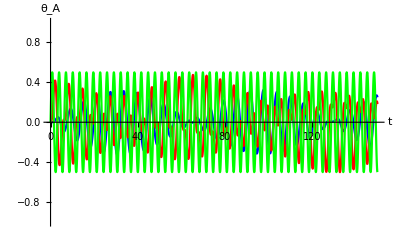

```mathematica
Shiv=Plot[F[t],{t,0,150},PlotRange->{-5,5},PlotStyle->Green];
a = ListPlot[data3c[[;;,{1,2}]],Joined->True,PlotStyle->Blue,AxesLabel->{t,Subscript[θ, A]},LabelStyle->Directive[Blue,Bold],PlotRange->{-1,1}];
b = ListPlot[data3c[[;;,{1,3}]],Joined->True,PlotStyle->Red,AxesLabel->{t,Subscript[θ, B]},LabelStyle->Directive[Blue,Bold],PlotRange->{-1,1}];
Show[a,b,Shiv]
```

#### Observation (3): This case we can observe that system is oscillating with bounded amplitude. hence we can conclude that our system is following F(w) Vs w plot perfectly. This case also steady state is not possible due to absence of damping force.

#### Physical System related to this Case: ?????????....................

## Case 4: Presence of Damping force and Driving force with initially spring at rest. a) ω < ω_0 b) ω ~ ω_0 (Resonance Condition) c) ω > ω_0

#### a) ω < ω_0

```mathematica
ω = 0.5;    F[t_]= (1)Sin[ω t] ;    initial4={0,0,0,0,0} ;    f= 0.7;
```

```mathematica
α=0.8;   
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data4a=rk4[{Id,taDot,tbDot,waDot,wbDot},initial4,100,5000];
```

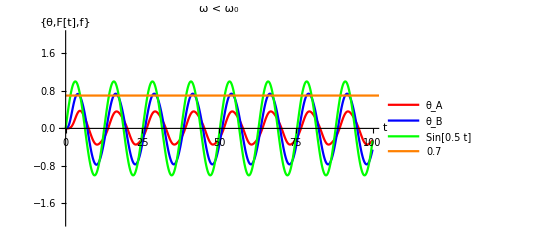

```mathematica
T1=ListPlot[data4a[[;;,{1,2}]],Joined->True,PlotStyle->Red,PlotRange->{-2,2},PlotLabel->"ω < ω_0 ",PlotLegends->{Subscript[θ, A]},AxesLabel->{t,{"θ","F[t]","f"}}];
T2=ListPlot[data4a[[;;,{1,3}]],Joined->True,PlotStyle->Blue,PlotRange->{-2,2},PlotLegends->{Subscript[θ, B]}];
Show[T1,T2,Plot[F[t],{t,0,100},PlotStyle->Green,PlotRange->{-2,2},PlotLegends->{F[t]}],Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

#### Observation: System Achieves Steady State after long time and oscillates with frequency of Driving Forces. Here we can observe amplitude of one pendulum attached to driving force is higher than other pendulum.

### Important Note regarding Limiting Case: In a Physical System with forced Oscillator and in the presence of damping force, It is important to choose proper damping condition and driving force combinations. If the driving force is very larger compared to damping force, then Amplitude response of oscillator will increase very fast and system will reach a steady state after very long time. Hence here damping force f ≥ 0.5 to achieve higher damping. Higher the damping force, more energy will be required to overcome the resistance and as a result system will lose energy quickly. Due to which amplitude of system will decrease.

#### b) ω ~ ω_0 (Natural Frequency of Coupled system is close to 1)

```mathematica
ω = 1.0;    F[t_]= (1)Sin[ω t] ;    initial4={0,0,0,0,0} ;    f= 0.7;
```

```mathematica
α=0.8;   
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data4b=rk4[{Id,taDot,tbDot,waDot,wbDot},initial4,100,5000];
```

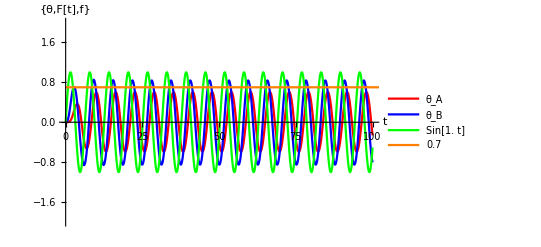

```mathematica
T1=ListPlot[data4b[[;;,{1,2}]],Joined->True,PlotStyle->Red,PlotRange->{-2,2},PlotLegends->{Subscript[θ, A]},AxesLabel->{t,{"θ","F[t]","f"}}];
T2=ListPlot[data4b[[;;,{1,3}]],Joined->True,PlotStyle->Blue,PlotRange->{-2,2},PlotLegends->{Subscript[θ, B]}];
Show[T1,T2,Plot[F[t],{t,0,100},PlotStyle->Green,PlotRange->{-2,2},PlotLegends->{F[t]}],Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

#### Observation: At resonance, We know system gains maximum energy. So amplitude of both the pendulum will be higher, which can be easily observed from plot. We can compare it to previous plot.

#### c) ω > ω_0

```mathematica
ω = 1.5;    F[t_]= (1)Sin[ω t] ;    initial4={0,0,0,0,0} ;    f= 0.7;
```

```mathematica
α=0.8;   
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data4c=rk4[{Id,taDot,tbDot,waDot,wbDot},initial4,100,5000];
```

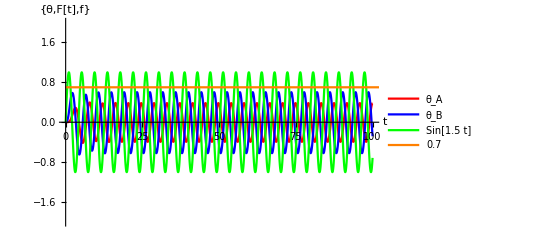

```mathematica
T1=ListPlot[data4c[[;;,{1,2}]],Joined->True,PlotStyle->Red,PlotRange->{-2,2},PlotLegends->{Subscript[θ, A]},AxesLabel->{t,{"θ","F[t]","f"}}];
T2=ListPlot[data4c[[;;,{1,3}]],Joined->True,PlotStyle->Blue,PlotRange->{-2,2},PlotLegends->{Subscript[θ, B]}];
Show[T1,T2,Plot[F[t],{t,0,100},PlotStyle->Green,PlotRange->{-2,2},PlotLegends->{F[t]}],Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

### Observation: 1) Again when driving frequency become larger then natural frequency of coupled oscillator there is again decrease in amplitude of pendulums. 2) At the beginning of Oscillation damping force is present. So we can observe that in combined plot of angular displacement with Driving force, angular frequency is not same. But after some time when system achieves steady state, it attains frequency of Driving Force.

### Physical System: RLC circuit with AC supply and for different values of Resistance(R Ω).

### Study of Various Driving Force Cases

## Case 5: Presence of Damping force and Constant Driving force with initially unstretched spring

```mathematica
F[t_]= 1;   f= 0.1;  initial5={0,0,0,0,0};
```

```mathematica
α=1;   
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data5a=rk4[{Id,taDot,tbDot,waDot,wbDot},initial5,100,5000];
```

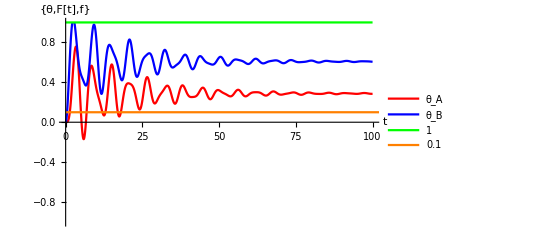

```mathematica
T1=ListPlot[data5a[[;;,{1,2}]],Joined->True,PlotStyle->Red,PlotRange->{-1,1},PlotLegends->{Subscript[θ, A]},AxesLabel->{t,{"θ","F[t]","f"}}];
T2=ListPlot[data5a[[;;,{1,3}]],Joined->True,PlotStyle->Blue,PlotRange->{-1,1},PlotLegends->{Subscript[θ, B]}];
Show[T1,T2,Plot[F[t],{t,0,100},PlotStyle->Green,PlotRange->{-1,1},PlotLegends->{F[t]}],Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

### Observation: 1) When Constant force is Applied to the system initially it will oscillates due to movement of block B and stretching of spring as We keep applying constant force system attains zero frequency as that of Constant force. Interesting Observation: Effect of KL/Mg (α) on the system: In our case both blocks have equal mass. I we keep K,L as constant then Higher mass implies low α value and vise a versa. for High α > 1 : As α is increasing from 1, then both oscillators start coming in phase of each other. For large α they are in phase with each other. This tell us that for block with less masses can easily come in phase of each other. for Low α < 1 : they are out of phase and far apart.

### Physical System: We can observe these types of oscillations when we lift two blocks (connected to each other by spring) by some constant force ‘F’. -Graphics-

## Case 6: Impulse Force (One of the Novel Case of Project) a) No damping force present b) Damping force present

#### a) When No damping force is present

-Graphics-

```mathematica
F[t_]= 2UnitStep[t]*UnitStep[1/10-t];    initial6a={0,0,0,0,0};f=0.0;
```

```mathematica
α=0.1;   
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data6a=rk4[{Id,taDot,tbDot,waDot,wbDot},initial6a,200,5000];
```

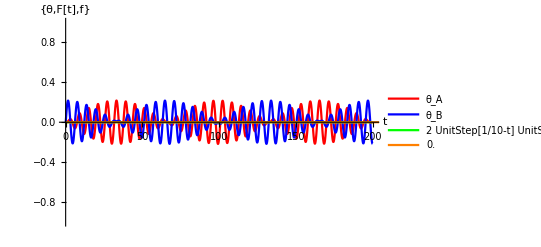

```mathematica
T1=ListPlot[data6a[[;;,{1,2}]],Joined->True,PlotStyle->Red,PlotRange->{-1,1},PlotLegends->{Subscript[θ, A]},AxesLabel->{t,{"θ","F[t]","f"}}];
T2=ListPlot[data6a[[;;,{1,3}]],Joined->True,PlotStyle->Blue,PlotRange->{-1,1},PlotLegends->{Subscript[θ, B]}];
Show[T1,T2,Plot[F[t],{t,0,200},PlotStyle->Green,PlotRange->{-1,1},PlotLegends->{F[t]}],Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

#### Observation : 1. Here System was in rest before bullet imparts impulse and after that it starts oscillating. Impulse is given to block B at time = 0 so it’s kinetic energy is max at t = 0 and for block ‘B’, K.E. is minimum so there is continuous energy transfer from one block to other without dissipation energy. We can observe some regular pattern after setting and playing with parameter α which is kL/Mg . Same Case of α we discussed before.

#### b) When Damping force is present

```mathematica
F[t_]= 1000UnitStep[t]*UnitStep[1/10-t];   f= 0.1;  initial6b={0,0,0,0,0};
```

```mathematica
α=0.1;   
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data6b=rk4[{Id,taDot,tbDot,waDot,wbDot},initial6b,250,5000];
```

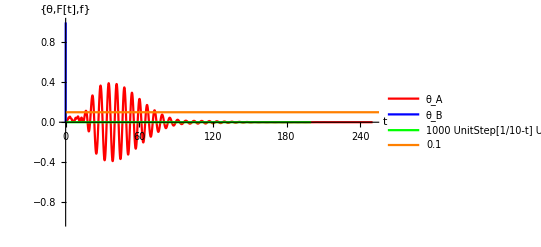

```mathematica
T1=ListPlot[data6b[[;;,{1,2}]],Joined->True,PlotStyle->Red,PlotRange->{-1,1},PlotLegends->{Subscript[θ, A]},AxesLabel->{t,{"θ","F[t]","f"}}];
T2=ListPlot[data6b[[;;,{1,3}]],Joined->True,PlotStyle->Blue,PlotRange->{-1,1},PlotLegends->{Subscript[θ, B]}];
Show[T1,T2,Plot[F[t],{t,0,200},PlotStyle->Green,PlotRange->{-1,1},PlotLegends->{F[t]}],Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

#### Observation: 1) We can observe decay of amplitude. First Sudden increase as system was disturbed from rest and then slowly system come in phase and then due to presence of damping force it starts decaying.

#### Physical System:This System is similar to imparting impulse by Bullet of small mass to Coupled block-spring mass system.

## Case: 7 friction Force due to hinge and absence of driving force

```mathematica
F[t_]=0;   f= 0.03 ;  initial7a={0,Pi/3,-Pi/3,0,0};
```

```mathematica
α=3;   
r[θa_,θb_]=Sqrt[(2 + Sin[θb]-Sin[θa])^2+(-Cos[θb]+Cos[θa])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
```

```mathematica
data7a=rk4[{Id,taDot,tbDot,waDot,wbDot},initial7a,120,5000];
```

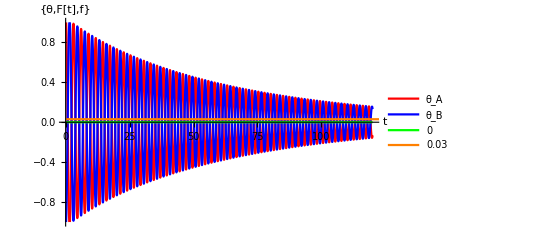

```mathematica
T1=ListPlot[data7a[[;;,{1,2}]],Joined->True,PlotStyle->Red,PlotRange->{-1,1},PlotLegends->{Subscript[θ, A]},AxesLabel->{t,{"θ","F[t]","f"}}];
T2=ListPlot[data7a[[;;,{1,3}]],Joined->True,PlotStyle->Blue,PlotRange->{-1,1},PlotLegends->{Subscript[θ, B]}];
Show[T1,T2,Plot[F[t],{t,0,120},PlotStyle->Green,PlotRange->{-1,1},PlotLegends->{F[t]}],Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

### Observation: 1. There is a constant decay of amplitude of pendulum. As the value of KL/Mg increases, number of oscillations increase.

## Case 8: Driving force Saw-Tooth wave (Skeletal Muscle movement mechanism)

### I. Overdamped. (f^2 > 4 ω_0^2)

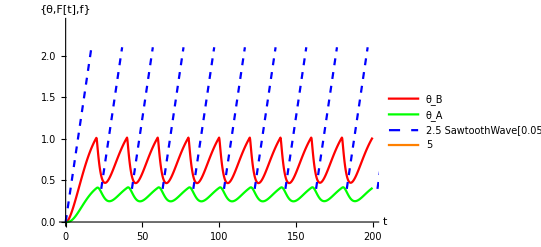

```mathematica
w=0.5;
α=1;
f = 5;
F[t_]= 2.5SawtoothWave[w t/10];
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,200,1000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{0,2.4},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],Plot[F[t],{t,0,10000},PlotStyle->{Dashed,Blue},PlotRange->All,PlotLegends->{F[t]}](*Time Vs Force*),
Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

Observations:
1. In this kind of system, the system Block B experiences higher amplitude as it experiences the direct impact of driving force.
2. Initially the system is at conditions θ_a = 0, θ_b= 0. As the driving force increases linearly, the amplitude increases to a peak point. As the force suddenly decreases the damping force takes over, thus giving a decaying oscillation.
3. But before the amplitude could decay all the way to zero, driving force starts increasing. Until the point where the driving force is less than the damping force, the system experiences decaying oscillations. But as soon as the driving force is greater the amplitude increases to the maximum value.
4. Block A experiences forces only due to the spring attached in between the two blocks. This reduces its amplitude significantly.

### Physical System: Force applied by Skeletal Muscle Fiber.

-Graphics-

#### Reference: 1. Skeletal Muscle Mechanics: From Mechanisms to Function. By W. Herzog II. Rief et. a.l ., 1997

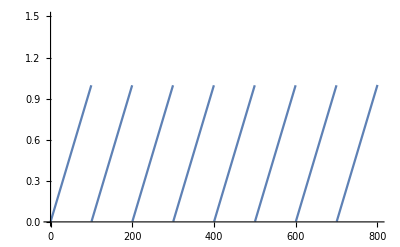

```mathematica
Plot[SawtoothWave[ 0.1 t/10],{t,0,800},PlotRange->{0,1.5}] (*Can be approximately fitted on the muscle fiber. *)
```

### II. Critically damped (f^2 = 4 ω_0^2)

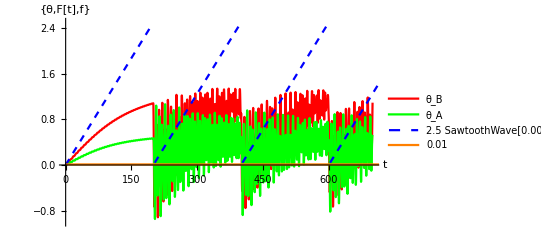

```mathematica
w=0.05;
α=1;
f= 0.01; 
F[t_]= 2.5SawtoothWave[w t/10];
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,700,2000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-1,2.5},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],Plot[F[t],{t,0,10000},PlotStyle->{Dashed,Blue},PlotRange->All,PlotLegends->{F[t]}](*Time Vs Force*),
Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

Observation: 
1. A saw tooth kind of driving force is applied to a system with the initial conditions θ_a= 0, θ_b = 0. As the driving force increases linearly with time, the amplitude also increases till it reaches a maximum. 
2. During the second cycle of force application the system is undergoing a harmonic motion with a continuously increasing force and hence an increasing amplitude.  
3. As the system progresses the amplitude keeps on increasing with each passing cycle of force. There will be a maximum amplitude (vertical position of blocks) after which the oscillations will no longer follow the harmonic/ anharmonic laws.

### III. Under Damped (f^2 < 4 ω_0^2)

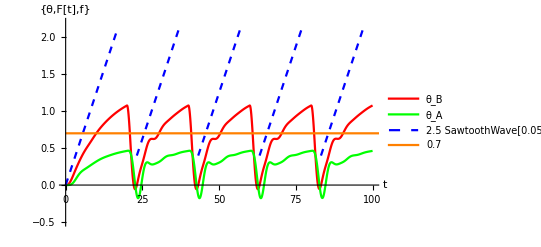

```mathematica
w=0.5;
α=1;
f = 0.7;
F[t_]=2.5 SawtoothWave[w t/10];
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,100,1000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-0.5,2.2},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],Plot[F[t],{t,0,10000},PlotStyle->{Dashed,Blue},PlotRange->All,PlotLegends->{F[t]}](*Time Vs Force*),
Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

### General Observations: 1. In the under damped condition, f^2< 4 w^2 is satisfied, and thus, the effect of the oscillations produced by the driving force F(t) with the frequency 'ω' dominates over the effect of the damping force due to air resistance. 2. Consider the Interval from t= 0 to 20 units. The force increases linearly in this interval on the block B, Thus, the

## Case 9: Exponentially decaying driving force.

### Initial Conditions: θ_a= 0, θ_b = 0. I. Overdamped (f^2> 4 ω_0^2)

0.03

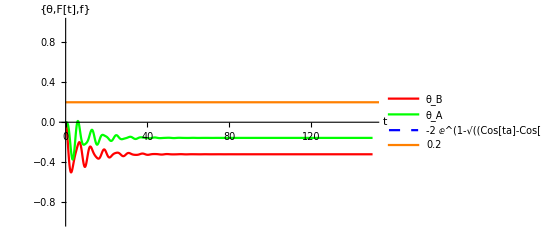

```mathematica
w=0.05;
α=1;
f =.2;
f^2- 4 w^2
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
F[t_]= -2 E^(1-r[ta,tb])(1-E^(1-r[ta,tb]));
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,150,5000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-1,1},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],
Plot[F[t],{t,0,10000},PlotStyle->{Dashed,Blue},PlotRange->All,PlotLegends->{F[t]}](*Time Vs Force*),
Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

Observation: 
1. For this kind of force application, the system experiences a force close to infinity as t is close to 0. Hence the amplitude shoots up. 
2. But the force amplitude decays too quickly due to an extremely high damping force (f = 5).
3. Thus the system does not undergoes even a complete oscillation.

### II. Critically damped (f^2= 4 ω_0^2)

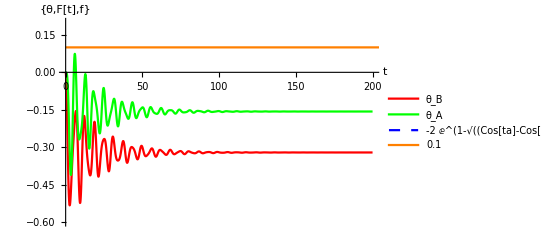

```mathematica
w=0.05;
α=1;
f= 2 w; 
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
F[t_]= -2 E^(1-r[ta,tb])(1-E^(1-r[ta,tb]));
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,200,5000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-0.6,0.2},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],
Plot[F[t],{t,0,10000},PlotStyle->{Dashed,Blue},PlotRange->All,PlotLegends->{F[t]}](*Time Vs Force*),Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

Observation: 
1. For this kind of force application, the system experiences a force close to infinity as t is close to 0. Hence the amplitude shoots up.
2. But now the resistive force is much lower than the previous case, hence system performs oscillations with gradually decaying amplitude.

### Initial Conditions: θ_a= 0, θ_b = 0. III. Under Damped (f^2< 4 ω_0^2)

-0.0099

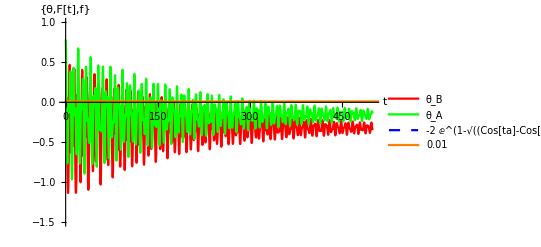

```mathematica
w=0.05;
α=1;
f = 0.01;
f^2- 4 w^2
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
F[t_]= -2 E^(1-r[ta,tb])(1-E^(1-r[ta,tb]));

wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,Pi/4,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,500,5000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-1.5,1},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],
Plot[F[t],{t,0,10000},PlotStyle->{Dashed,Blue},PlotRange->All,PlotLegends->{F[t]}](*Time Vs Force*),
Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

Observations:
1. Amplitudes of both the blocks increases with time, reaches a maximum value of around 0.47. 
2. After this point the driving force is much less than the resistive force. Hence the system is unable to complete further oscillations. And the amplitude dies down to zero.
Resistive force >> Driving force.

Physical Significance:
1)As mentioned in the introduction, Anharmonicity plays a role in lattice and Di-molecular vibrations. The atoms in a molecule or a solid vibrate about their equilibrium positions. When these vibrations have small amplitudes they can be described by harmonic oscillators. However, when the vibrational amplitudes are large, for example at high temperatures, anharmonicity becomes important.
The potential function given for the same is:
V_M( r ) = D_e[ 1 − e^(− β (r − r_e))].Where,
V_M is the potential energy of a diatomic molecule with interatomic distance r and equilibrium bond length r_e , D_e is the well depth, and β is a parameter that governs the width of the Morse function well.

## Case 10: Unit step driving force. (Bullet Impulse)

#### I. Over damped. (f^2> 4 ω_0^2)

Physical System :- Impulse.

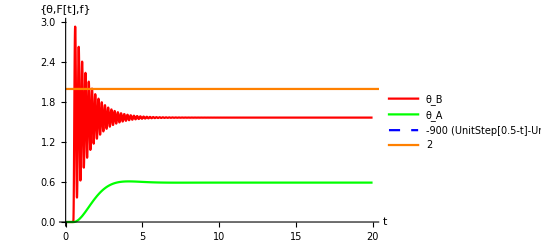

```mathematica
w=0.5;
α=1;
f = 2;
F[t_]= -900 (UnitStep[0.5-t] - UnitStep[t]);
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,20,5000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{0,3},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],Plot[F[t],{t,0,10000},PlotStyle->{Dashed,Blue},PlotRange->All,PlotLegends->{F[t]}],
Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

Observation: 
1. Here amplitude suddenly shoots up at the end of force application.
2. As the driving force dies out, the system performs normal damped oscillations.

#### II. Critically damped. (f^2> 4 ω_0^2)

Physical System :- Impulse.

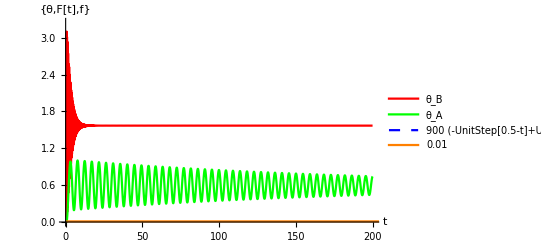

```mathematica
w=0.05;
α=1;
f= 0.01; 
F[t_]=  900(UnitStep[t]-UnitStep[0.5-t]  );
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,200,5000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{0,3.25},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],
Plot[F[t],{t,0,10000},PlotStyle->{Dashed,Blue},PlotRange->All,PlotLegends->{F[t]}],
Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

Observations:
1.  Here block A performs oscillations as if it were under a constant spring force, its amplitude decreases due to the resistive force term “ f ”.
2. Oscillations of Block B are much more pronounced due to sudden application of an infinite force which then gradually decreases.

#### III. Under damped. (f^2< 4 ω_0^2)

Physical System :- Impulse.

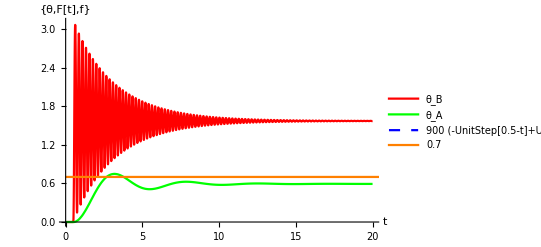

```mathematica
w=0.5;
α=1;
f = 0.7;
F[t_]=  900(UnitStep[t]-UnitStep[0.5-t]  );
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,20,5000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{0,3.1},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],Plot[F[t],{t,0,10000},PlotStyle->{Dashed,Blue},PlotRange->All,PlotLegends->{F[t]}],
Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

Observations:
1. In this kind of driving force, block B experiences maximum force and it completes multiple decaying oscillations. 
2. Block A on the other hand undergoes a single oscillation before completely dying out.

## Case 11: Triangular waves

#### I. Over damped. (f^2> 4 ω_0^2)

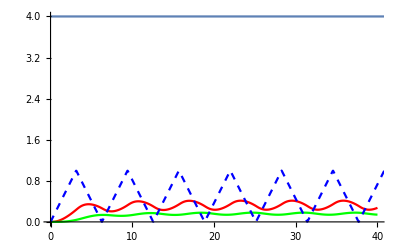

```mathematica
w=0.5;
α=1;
f = 4;
F[t_]=Abs[2/Pi ArcSin[Sin[w t]]];
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,40,5000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{0,4}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All(*Time Vs ta*)],Plot[F[t],{t,0,100},PlotStyle->{Dashed,Blue},PlotRange->All](*Time Vs Force*),
Plot[f,{t,0,100}]]
```

#### II. Critically damped. (f^2= 4 ω_0^2)

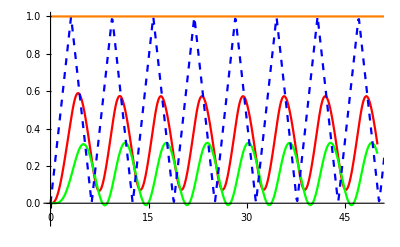

```mathematica
w=0.5;
α=1;
f= 1; 
F[t_]=Abs[2/Pi ArcSin[Sin[w t]]];
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,50,5000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-0.1,1}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All(*Time Vs ta*)],Plot[F[t],{t,0,300},PlotStyle->{Dashed,Blue},PlotRange->All](*Time Vs Force*),
Plot[f,{t,0,400},PlotStyle->Orange]]
```

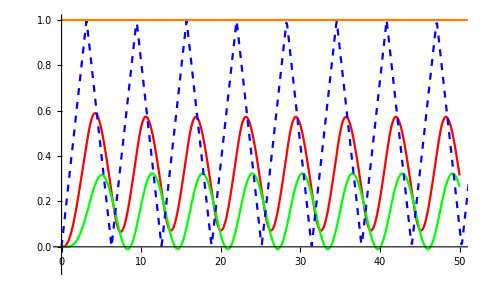
Observations: For Critically Damped
1. For a particular set of values of α,w and f we get a Plot in which θ_A and θ_B and Driving Force are in Phase
2. We applied Triangular wave as our F(t).Consider the interval from t = 0 to 30 units. The Force applied horizontally on Block B increases linearly and thus, this leads to a jump in the value of θ_Band the stretching of the spring which in turn makes the Block B vibrate on the right side of the vertical .As the Block A is attached to the Block B with a spring, the Block A also undergoes a synchronized increase in the θ_A just as θ_B increases due to a linear force rightward.
3. In the interval t = 30 to 60, a linearly decreasing force is applied on Block B leftward.SImilarly the angular displacement Block A increases leftward but with a lower amplitude than B because the 2 blocks are attached with a spring.
4. When initial conditions are applied to θ_A, this disturbs the system for the first 60 units of time, but later the 2 blocks oscillate in sync 
The Block B shall also vibrate with the same frequency as the Block A because in the free body diagram of Block B,  
5. Increasing value of α=Kl/Mg, magnitude of θ_A and θ_B gets closer to one another as the ω1=√(K/M)starts dominating over ω2=√(g/l).Note that ω1 is the frequency of oscillation of the Spring and ω2 is the oscillation of the Block suspended with a string in case of the absence of the0 spring.As ω1 increases, it directly means that the spring in action between the 2 blocks becomes more stiff, which inturn decreases the disparity between the amplitude of vibration of the 2 blocks.
-Graphics-  α=10
This is the above plot is for α=Kl/Mg=1.  This plot is for,α=Kl/Mg=10.

6. Sharpness of plot increases as the damping constant increases, and a time lag is developed due to the applied damping force.Thus the peaks of both the blocks are shifted towards the right of the mean (as set by the applied force (F(t)).
7. In the over damped case, the as the condition f^2>4 w^2 is satisfied, Here the damping effects dominate over the effects on the oscillation of the system due to the driving force F(t).
As compared to the plot of F(t), the peaks of the values of θ_A and θ_B is shifted and suffer a time lag due to he high damping coefficient and the Plot of θ_A has 
a much lower amplitude of vibration.
8. In the under damped case, the as the condition f^2<4 w^2 is satisfied, and thus  the effects of the driving force on the oscillation of the system dominate over the damping effects produced. Thus ,high amplitude of oscillaion for Block B .The oscillation of Block A has a delay as compared to the Block B because of the stiffness of the spring.
9. Also note that ,the amplitude of θ_A and θ_B is majorly on the positive side i.e the right side of the mean, because the initial force, applied was to the right side.
Refer: http://hyperphysics.phy-astr.gsu.edu/hbase/oscda2.html

#### III. Under damped. (f^2< 4 ω_0^2)

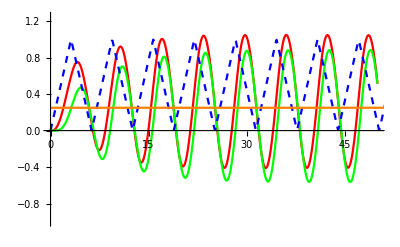

```mathematica
w=0.5;
α=1;
f = 0.25;
F[t_]=Abs[2/Pi ArcSin[Sin[w t]]];
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,50,5000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-1,1.25}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All(*Time Vs ta*)],Plot[F[t],{t,0,300},PlotStyle->{Dashed,Blue},PlotRange->All](*Time Vs Force*),
Plot[f,{t,0,70},PlotStyle->Orange](*Resistive force*)]
```

### When no damping is present.

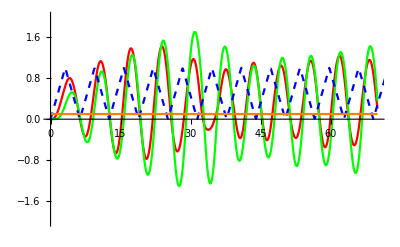

```mathematica
w=0.5;
α=1;
f = 0.1;
F[t_]=Abs[2/Pi ArcSin[Sin[w t]]];
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,70,5000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-2,2}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All(*Time Vs ta*)],Plot[F[t],{t,0,300},PlotStyle->{Dashed,Blue},PlotRange->All](*Time Vs Force*),
Plot[f,{t,0,70},PlotStyle->Orange](*Resistive force*)]
```

## Case 12: Driving Force is of a Theta Kind

#### I. Over damped. (f^2> 4 ω_0^2)

```mathematica
w=0.015;
α=1;
f=0.1;
F[t_]=1/4(HeavisideTheta[-1/2+Cos[w t]]);
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,1000,5000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-0.2,0.4},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],Plot[F[t],{t,0,1000},PlotStyle->{Dashed,Blue},PlotLegends->{F[t]},PlotRange->All],Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}](*Time Vs Force*)]
```

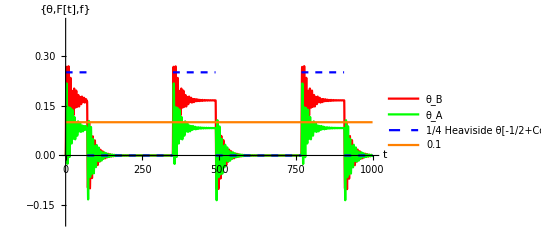

>

Observations
1. For initial period of time system behaves as if it is under a constant driving force and constant damping coefficient ,after that it just behaves like as if both blocks were released from some θ_Aand some θ_B.
2. For small  value of ‘ f ’ ,the damping constant, the difference between the 2 amplitudes 
We applied a constant force as our F(t).Consider the interval from t = 0 to π/(3 w)(=69.8132) units where the w=0.015 and a non zero constant force is applied . The Force applied horizontally only on Block B is constant and thus, this leads to a jump in the value of θ_(B .)The stretching of the spring leads to the oscillation of the of the Block A with a damping coefficient (f=0.01).Whereas, the amplitude of oscillation for  both Block B and Block A will  be same. The  shifted mean axis about which the oscillations would take place for Block B and Block A would be Different.The mean axis for Block B would be at greater angle with vertical than block a till constant force is applied. 
Now consider the case when the applied force reduces to zero after t=69.8132 units.
 In this case, the mean axis about which oscillations of Block B and BlockA  takes place would be restored to the initial and the two  Blocks would start oscillating in resonance with each other about the mean axis but both the  blocks would suffer  damping in their amplitude due to hinge.

#### II. Critically damped. (f^2= 4 ω_0^2)

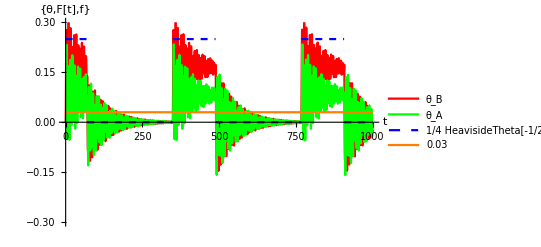

```mathematica
w=0.015;
α=1;
f= 0.03; 
F[t_]=1/4(HeavisideTheta[-1/2+Cos[w t]]);
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,1000,5000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-.3,.3},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],Plot[F[t],{t,0,1000},PlotStyle->{Dashed,Blue},PlotLegends->{F[t]},PlotRange->All](*Time Vs Force*),
Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

#### III. Under damped. (f^2< 4 ω_0^2)

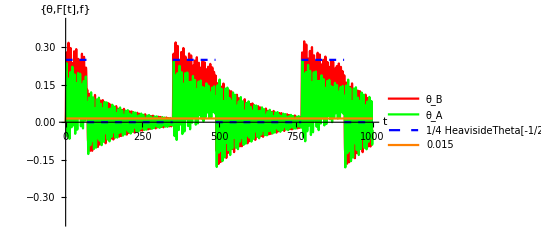

```mathematica
w=0.015;
α=1;
f = 0.015;
F[t_]=1/4(HeavisideTheta[-1/2+Cos[w t]]);
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,0,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,1000,5000];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-.4,.4},AxesLabel->{t,{"θ","F[t]","f"}},PlotLegends->{Subscript[θ, B]}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],Plot[F[t],{t,0,1000},PlotStyle->{Dashed,Blue},PlotRange->All,PlotLegends->{F[t]}](*Time Vs Force*),
Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

## Case 13: Electrostatic Driving Force

If we consider that the Block B has a fixed charge of +Q and a ball with a charge -Q fixed on it starts from x_0=1 units, where x_0 is the initial separation of the Block B and the ball with a negative charge.

#### I. Over damped. (f^2> 4 ω_0^2)

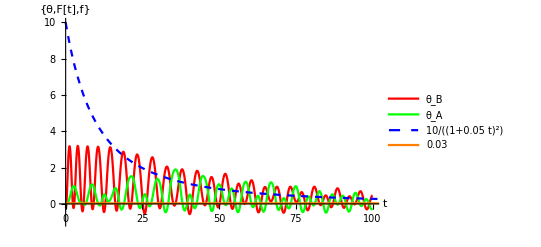

```mathematica
w=0.05;
α=1;
f= 0.03;
F[t_]= 10/(1+w t)^2;
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,-Pi/12,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,100,7000];
 
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-1,10},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],Plot[F[t],{t,0,1000},PlotStyle->{Dashed,Blue},PlotLegends->{F[t]},PlotRange->All](*Time Vs Force*),
Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

>Observations

#### II. Critically damped. (f^2= 4 ω_0^2)

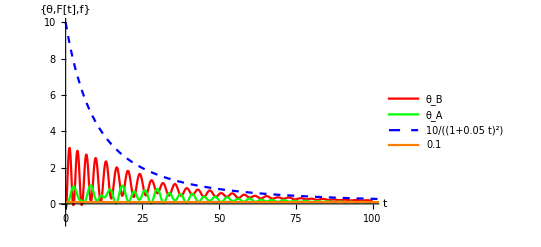

```mathematica
w=0.05;
α=1;
f= 2 w;
F[t_]= 10/(1+w t)^2;
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,-Pi/12,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,100,7000];

Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-1,10},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],Plot[F[t],{t,0,1000},PlotStyle->{Dashed,Blue},PlotLegends->{F[t]},PlotRange->All](*Time Vs Force*),
Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```

#### III. Under damped. (f^2< 4 ω_0^2)

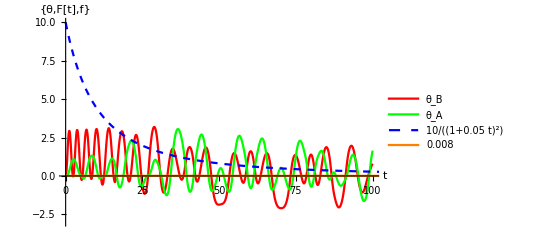

```mathematica
w=0.05;
α=1;
f= 0.008;
F[t_]= 10/(1+w t)^2;
r[ta_,tb_]=Sqrt[(2 + Sin[tb]-Sin[ta])^2+(-Cos[tb]+Cos[ta])^2];
Id[t_,ta_,tb_,wa_,wb_]=1;
taDot[t_,ta_,tb_,wa_,wb_]=wa;
tbDot[t_,ta_,tb_,wa_,wb_]=wb;
waDot[t_,ta_,tb_,wa_,wb_]=-Sin[ta]+ α (1-2/r[ta,tb])*(2 Cos[ta]-Sin[ta-tb]) -f wa;
wbDot[t_,ta_,tb_,wa_,wb_]= -Sin[tb]+F [t]Cos[tb]+ α(1-2/r[ta,tb])*(-2 Cos[tb]+Sin[ta-tb])-f wb;
initial={0,0,-0.02,0,0};
data=rk4[{Id,taDot,tbDot,waDot,wbDot},initial,100,5000];
 
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,PlotRange->{-3,10},PlotLegends->{Subscript[θ, B]},AxesLabel->{t,{"θ","F[t]","f"}}(*Time Vs tb*)],ListPlot[data[[;;,{1,2}]],Joined->True ,PlotStyle->Green,PlotRange->All,PlotLegends->{Subscript[θ, A]}(*Time Vs ta*)],Plot[F[t],{t,0,1000},PlotStyle->{Dashed,Blue},PlotLegends->{F[t]},PlotRange->All](*Time Vs Force*),
Plot[f,{t,0,1000},PlotStyle-> Orange,PlotLegends-> {f}]]
```